## 2.4 Spezialfälle und Veranschaulichung von Funktionen f : U ⊂ R^n -> R^m

### 2.4.(i) Kurven (n=1)

#### m = 2; Ebene Kurven

```mathematica
Der Befehl zum Plotten von Kurven im R^2 (ebenen Kurven) heisst 
ParametricPlot
```

```mathematica
?ParametricPlot
```

RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a parametric plot of a curve with StyleBox["x", "TI"] and StyleBox["y", "TI"] coordinates SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]] and SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]] as a function of StyleBox["u", "TI"]. 
RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["g", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several parametric curves. 
RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots a parametric region. 
RowBox[{"ParametricPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["g", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["v", "TI"], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several parametric regions.

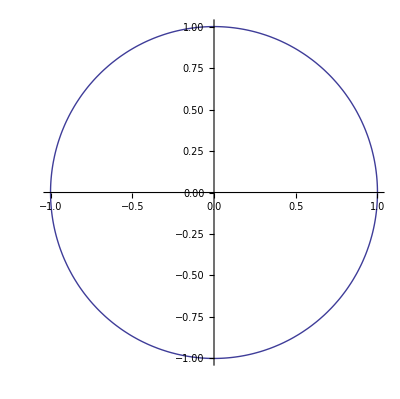

```mathematica
c[t_]:={Cos[t],Sin[t]}
ParametricPlot[c[t],{t,0,2*Pi}]
```

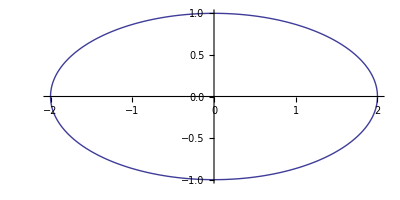

```mathematica
alpha[t_]:={2Cos[t],Sin[t]}
ParametricPlot[alpha[t],{t,0,2Pi}]
```

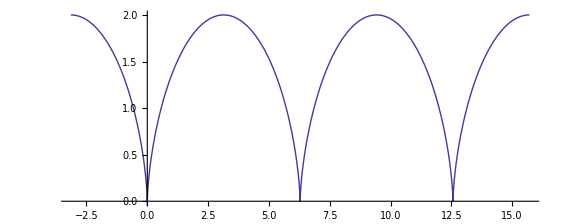

```mathematica
s[t_]:={t-Sin[t],1-Cos[t]}
ParametricPlot[s[t],{t,-Pi,5Pi}]
```

Eine Animation zur Enstehung der Zykloide als Rollkurve : Die Zykloide beschreibt die Bewegung eines Randpunktes eines rollenden Rads

```mathematica
Animate[ParametricPlot[{{s t/(2 Pi)-Sin[s t/(2 Pi)],1-Cos[s t/(2 Pi)]},{s+Cos[t],1+Sin[t]}},{t,0,2 Pi},AspectRatio->Automatic,(*same scale for x-and y-axis*)PlotRange->{{-1,6Pi+1.2},{-1,3}}],(*same range for all frames*){s,0,6Pi}]
```

### m = 3; Raumkurven

Der Befehl zum Plotten von Kurven im R^3 (Raumkurven) heisst 
ParametricPlot3D

```mathematica
?ParametricPlot3D
```

ParametricPlot3D[{f_x,f_y,f_z},{u,u_min,u_max}] produces a three-dimensional space curve parametrized by a variable u which runs from u_min to u_max. 
ParametricPlot3D[{f_x,f_y,f_z},{u,u_min,u_max},{v,v_min,v_max}] produces a three-dimensional surface parametrized by u and v. 
ParametricPlot3D[{{f_x,f_y,f_z},{g_x,g_y,g_z}…}…] plots several objects together.

```mathematica
c[t_] := {Cos[t], Sin[t], t}
ParametricPlot3D[c[t], {t, 0, 4 Pi}]
```

-Graphics3D-

### 2.4 (ii) Landschaften (n=2, m=1)

```mathematica
Ber Basisbefehl zum Plotten des Graphen einer Funktion U⊂R^2->R lautet Plot3D, der Befehl zur Darstellung der Höhenschichtlininen CountourPlot
```

```mathematica
?Plot3D
?ContourPlot
```

RowBox[{"Plot3D", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a three-dimensional plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] and StyleBox["y", "TI"]. 
RowBox[{"Plot3D", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions.

RowBox[{"ContourPlot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a contour plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] and StyleBox["y", "TI"]. 
RowBox[{"ContourPlot", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "==", StyleBox["g", "TI"]}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots contour lines for which RowBox[{StyleBox["f", "TI"], "=", StyleBox["g", "TI"]}]. 
RowBox[{"ContourPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], "==", SubscriptBox[StyleBox["g", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], "==", SubscriptBox[StyleBox["g", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several contour lines.

-Graphics3D-

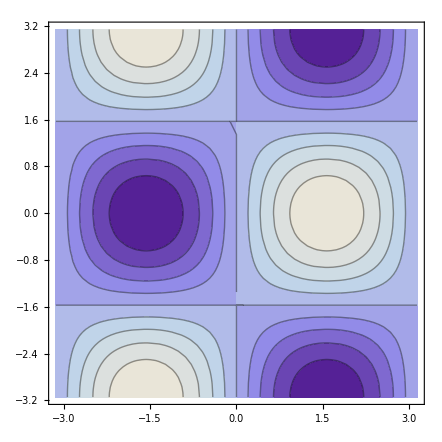

```mathematica
f[x_,y_]:=Sin[x]*Cos[y]
Plot3D[f[x,y],{x,-Pi,Pi},{y,-Pi,Pi}]
ContourPlot[f[x,y],{x,-Pi,Pi},{y,-Pi,Pi}]
```

### 2.4 (iii) Vektorfelder (n=m)

#### n = 2 = m

```mathematica
Der Basisbefehl zum Plotten von Vektorfeldern im R^2 lautet VectorPlot.
```

```mathematica
?VectorPlot
```

VectorPlot[{v_x,v_y},{x,x_min,x_max},{y,y_min,y_max}] generates a vector plot of the vector field {v_x,v_y} as a function of x and y. 
VectorPlot[{{v_x,v_y},{w_x,w_y},…},{x,x_min,x_max},{y,y_min,y_max}] plots several vector fields.

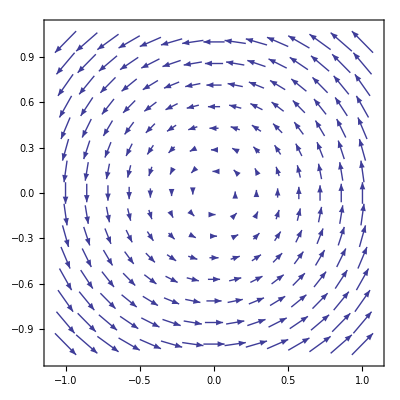

```mathematica
v[x_,y_]:={-y,x}
VectorPlot[v[x,y],{x,-1,1},{y,-1,1}]
```

#### n = 3 = m

```mathematica
Vektorfelder im R^3 werden von (erraten!) VectorPlot3D erzeugt.
?VectorPlot3D
```

VectorPlot3D[{v_x,v_y,v_z},{x,x_min,x_max},{y,y_min,y_max},{z,z_min,z_max}] generates a 3D vector plot of the vector field {v_x,v_y,v_z} as a function of x, y and z.
VectorPlot3D[{field_1,field_2,…},{x,x_min,x_max},{y,y_min,y_max},{z,z_min,z_max}] plots several vector fields.

im R^3 VectorPlot3D Vektorfelder von werden erzeugt.Null erraten!

```mathematica
w[x_,y_,z_]:={x,y,z}
VectorPlot3D[w[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-